## Z-Matrix Derivatives

### Z-Matrix to Cartesian

We do so much work with Z-matrices and Cartesians that we should really have an analytic representation of the Jacobian. So let’s get on that. We’ll start by going from Z-matrix to Cartesian. To do that we note that we need 3 pieces of info

The origin x_0, can be assumed to be (0, 0, 0) by default

The axis system (e_1, e_2, e_3), can be assumed to be I_3 (well really e_3 actually isn’t necessary)

The Z-matrix

For every atom, our Z-matrix tells us 6 things

What are the reference positions, x_(i-1), x_(i-2), x_(i-3)

What are the reference values, z_(i,1), z_(i,2), z_(i,3)

#### Derivation

We define our coordinates recursively as

v_i=x_(i,b)-x_(i,a) u_i=x_(i,c)-x_(i,a) n_i=v_i×u_i
x_i=x_(i,a)+R(z_(i,3), v_i)·R(z_(i,2), n_i)·z_(i,1)(v̂)_i

where R(θ,v) is a rotation of θ radians about axis v̂, given by

R(θ, v)=(cosθ | -v_zsinθ | v_y sinθ
v_z sinθ | cosθ | -v_xsinθ
-v_ysinθ | v_x sinθ | cosθ)+(v_x^2 | v_x v_y | v_x v_z
v_x v_y | v_y^2 | v_y v_z
v_x v_z | v_y v_z | v_z^2)(1-cosθ)
=(v_x^2 | v_x v_y | v_x v_z
v_x v_y | v_y^2 | v_y v_z
v_x v_z | v_y v_z | v_z^2)+(0 | -v_z | v_y
v_z | 0 | -v_x
-v_y | v_x | 0)sinθ+(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)cosθ+
=v̂⊗v̂+(𝕀_3-v̂⊗v̂)cos(θ)-ϵ_3 v̂ sin(θ)

which I’ll agree is not the most intuitive thing in the world, but maybe is a bit nice to think about when you know that it comes from the Rodrigues rotation formula

R(θ, k).v = cosθ v + sinθ (k×v) + (k·v) (1-cosθ)k

I think that’s definitely got a clearer physical meaning you can work with.

In any case, this means we get

(d x_i)/dq=(d x_(i-1))/dq+d/dq(z_(i,1)R(z_(i,3), v_i)·R(z_(i,2), n_i)·(v̂)_i)

where q is one of our z_nm components.

It’s worth noting that we have to compute this recursively, i.e. we need the i-1 result before we can get the i result. When implementing, keep in mind that the parts of rotation derivatives can be computed without knowing the i-1 results, though.

First off, for chain-rule reasons we’ll condense the rotation matrices into a single rotation

Θ=R(z_(i,3), v_i)·R(z_(i,2), n_i)

which means that we get

(d x_i)/dq=(d x_(i-1))/dq+(d/dq Θ)·(v̂)_i+Θ·d/dq(v̂)_i
=(d x_(i-1))/dq+(d/dq Θ)·(v̂)_i+Θ·((d(v̂)_i)/dq)

then since q is scalar, the product rule applies as normal so we get

d/dq Θ=(d/dq R(z_(i,3), v_i))·R(z_(i,2), n_i)+R(z_(i,3), v_i)·d/dqR(z_(i,2), n_i)

next we’ll look at one of these rotations on its own, like

d/dq R(θ, v)=d/dq(v⊗v)+d/dq(𝕀_3-v⊗v)cos(θ)-d/dq ϵ_3 vsin(θ)
=v'⊗v+v⊗v'+(d(𝕀_3-v⊗v))/dq cos(θ)-(𝕀_3-v⊗v)sin(θ)dθ/dq-ϵ_3(dv/dq sin(θ)+vcos(θ)dθ/dq)
=v'⊗v+v⊗v'-(v'⊗v+v⊗v')cos(θ)-(𝕀_3-v⊗v)sin(θ)θ'-ϵ_3(v'sin(θ)+vcos(θ)θ')

I’m sure this looks nasty, but most of this is actually pretty straightforward. To justify this claim, let’s note that either v=v_i or v=n_i, θ=z_(i,2) or θ=z_(i,3), and

d/dq â=1/(|a|)da/dq-a/(|a|)^2 d/dq √(a·a)
=1/(|a|)da/dq-a/(|a|)^3 da/dq·a
=1/(|a|)(da/dq-â da/dq·â)
=1/(|a|)(𝕀_3-â⊗â)da/dq
d/dq u_i=(d x_(i,b))/dq-(d x_(i,a))/dq
d/dq u_i=d/dq(x_(i,c)-x_(i,a))=(d x_(i,c))/dq-(d x_(i,a))/dq
d/dq n_i=d/dq v_i×u_i=d/dq v_i×u_i+v_i×d/dq u_i
(d z_(i,2))/dq=δ_(q z_(i,2))
(d z_(i,3))/dq=δ_(q z_(i,3))

and we’ve got dx_(i,a)/dq, dx_(i,b)/dq and dx_(i,c)/dq from prior steps.

I’m not gonna write this out in full, though, since that’s just asking for me to make a mistake.

Finally, let’s think about the case that we have

(d x_i)/(d z_nm)=(d x_(i,a))/(d z_nm)+(d/(d z_nm)Θ)·(v̂)_i+Θ·d/(d z_nm)(v̂)_i

we’ll note that we have

(d z_ij)/(d z_nm)=0

but recursively, we can still have

(d x_(i,a))/(d z_nm)≠0

##### A Note on Formatting

A way I like to think about this is in terms of blocks matrices, where

∇_Z X=(∇_Z_1 x_0 | ∇_Z_1 x_1 | ∇_Z_1 x_2 | ∇_Z_1 x_3
∇_Z_2 x_0 | ∇_Z_2 x_1 | ∇_Z_2 x_2 | ∇_Z_2 x_3
∇_Z_3 x_0 | ∇_Z_3 x_1 | ∇_Z_3 x_2 | ∇_Z_3 x_3)

#### Implementation

##### Correct Answer

```mathematica
correctAns=;
correctAnsSpec=;
zCoords=;
```

##### Code

```mathematica
zmatDerivsC=
With[{ee=Normal@LeviCivitaTensor[3]},
Compile[{
{zmCoords, _Real, 2},
{spec, _Integer, 2},
{origin, _Real,1},
{xAxis, _Real,1},
{yAxis, _Real, 1}
},
Block[
{
zeroMat=Table[0., {i, 3}, {j, 3}], 
zeroVec=Table[0., {i, 3}]
},
Block[
{
coords=Table[0., {i, Length[spec]+1}, {j, 3}],
derivs=Table[0., {i, Length[spec]+1}, {j, 3}, {k, Length[spec]+1}, {l, 3}],
r, q, f,
ia, ib, ic,
vi=zeroVec, ui=zeroVec, ni=zeroVec,
nvi=0.,nui=0.,nni=0.,
R1, R2,Q,
dR1, dR2,
drn,dqn,dfn,
xi1=zeroVec, xi2=zeroVec, xi3=zeroVec,
dxi1=zeroVec, dxi2=zeroVec, dxi3=zeroVec,
dv=zeroVec, du=zeroVec,dni=zeroVec,
dQ=zeroMat,
i3=IdentityMatrix[3],
e3=ee
},
coords[[1]]=origin;
Do[
{r, q, f}=zmCoords[[i, {1, 2, 3}]];
{ia, ib, ic}= spec[[i, {2, 3, 4}]];
(* choose prior coordinates based on passed spec *)
xi1=coords[[ia]];
If[i>1,xi2=coords[[ib]], xi2=zeroVec];
If[i>2,xi3=coords[[ic]], xi3=zeroVec];
(* generate current coord *)
If[i>1,vi= xi2-xi1,vi=xAxis];
nvi=Sqrt[Total[vi^2]];vi/=nvi;
If[i>2,ui=xi3-xi2,ui=yAxis];
nui=Sqrt[Total[ui^2]];ui/=nui;
ni=Cross[vi, ui];nni=Sqrt[Total[ni^2]];ni/=nni;
R1=Outer[Times, vi, vi]
+(i3-Outer[Times, vi, vi])*Cos[f]
-Dot[e3, vi]*Sin[f];
R2=Outer[Times, ni, ni]
+(i3-Outer[Times, ni, ni])*Cos[q]
-Dot[e3, ni]*Sin[q];
Q=R1.R2;
coords[[i+1]]=xi1+Q.(r*vi);
Do[
If[ia>1, dxi1 =derivs[[n,m, ia-1]],dxi1 =zeroVec];
If[ib>1, dxi2 =derivs[[n, m,ib-1]],dxi2 =zeroVec];
If[ic>1, dxi3 =derivs[[n, m,ic-1]],dxi3 =zeroVec];
If[i>1,
dv= dxi2-dxi1;
dv=1/nvi*(dv-vi*Dot[dv, vi]),
dv=zeroVec
];
If[i>2,
du=dxi3-dxi2;
du=1/nui*(du-ui*Dot[du, ui]);, 
du=zeroVec
];
drn=n==i&&m==1;
dqn=n==i&&m==2;
dfn=n==i&&m==3;
If[i>1,
dni=Cross[dv, ui]+Cross[vi, du];
dni=1/nni*(dni-ni*Dot[dni, ni]);
(* generate terms in deriv expression *)
dR2=
Outer[Times, dni, ni]+Outer[Times, ni, dni]
-(Outer[Times, dni, ni]+Outer[Times, ni, dni])*Cos[q]
-If[dqn, (i3-Outer[Times, ni, ni])*Sin[q],zeroMat]
-Dot[e3, dni]* Sin[q]
-If[dqn, Dot[e3, ni]*Cos[q], zeroMat];
If[i>2,
dR1=
Outer[Times, dv, vi]+Outer[Times,vi, dv]
-(Outer[Times, dv, vi]+Outer[Times, vi, dv])*Cos[f]
-If[dfn, (i3-Outer[Times, vi, vi])*Sin[f],  zeroMat]
-Dot[e3, dv]*Sin[f]
-If[dfn, Dot[e3, vi]*Cos[f], zeroMat];
dQ=dR1.R2+R1.dR2,
If[i==2,
dQ=R1.dR2,
dQ=ConstantArray[0., {3, 3}]
]
]
];
derivs[[n, m, i]]=
dxi1+If[i>1,
Dot[dQ, r*vi]+Dot[Q, If[drn, vi, zeroVec]+r*dv],
If[drn, vi, zeroVec]
];
(*If[n==2&&m==2,
Echo[
MatrixForm/@{
{r,q,f}, 
{vi, ui, ni},
{dv, du, dni}, Q, dQ, 
dxi1,
Total@{Dot[dQ, r*vi],Dot[Q,r*dv]},
{Dot[dQ, r*vi],Dot[Q,r*dv]}
}, {{n, m}, i}]
];*),
{n, i},
{m, 3}
],
{i, 1, Length[spec]}
];
derivs[[-1, 1]]=coords;
derivs
]
]
]
];
```

```mathematica
zmatDerivs//Clear
zmatDerivs[
zmCoords_, spec_, 
Optional[{origin_, {xAxis_, yAxis_}}, {{0., 0., 0.}, {{1., 0., 0.}, {0., 1., 0}}}]
]:=
With[{cRes=zmatDerivsC[zmCoords, spec, origin, xAxis, yAxis]},
{
cRes[[-1, 1]],
ArrayReshape[cRes[[;;-2, ;;, ;;-2, ;;]], {Length[spec]*3, Length[spec]*3}]
}
]
```

### Cartesian to Z-Matrix

#### Derivation

For this we only have three types of things to calculate

Bond distances

Bond angles

Dihedral angles

so if we can get expressions for each of these we’re golden. Unfortunately the expressions are still super annoying to work with.

In this case we have

r_ij=|a| | where a=x_j-x_i
θ_ijk=arctan2((|a×b|)/(|a||b|), (a·b)/(|a||b|)) | where a=x_j-x_i and b=x_k-x_i
τ_ijkl=arctan2((n̂)_1·(n̂)_2, ((n̂)_1×b̂)·(n̂)_2) | where a=x_j-x_i, b=x_k-x_j, c=x_l-x_k
(n̂)_1=(a×b)/(|a×b|), (n̂)_2=(b×c)/(|b×c|), b̂=b/(|b|)

Case 1: r

so for our r terms we have

r_ij=|x_j-x_i|=√((x_j-x_i)·(x_j-x_i))
(∂r_ij)/(∂x_nm)=(∂(x_j-x_i)·(x_j-x_i))/(∂x_nm__)1/(2 √((x_j-x_i)·(x_j-x_i)))
=((∂(x_j-x_i))/(∂x_nm__)·(x_j-x_i)+(x_j-x_i)·(∂(x_j-x_i))/(∂x_nm__))1/(2 √((x_j-x_i)·(x_j-x_i)))
=((∂(x_j-x_i))/(∂x_nm__)·(x_j-x_i))1/(|x_j-x_i|)

this is a bit weird to think about, given that these are vector quantities, but we can expand them out in terms of their components to get

(∂(x_j-x_i))/(∂x_nm__)=(∂x_j)/(∂x_nm)-(∂x_i)/(∂x_nm)
=((∂x_j1)/(∂x_nm)-(∂x_i1)/(∂x_nm), (∂x_j2)/(∂x_nm)-(∂x_i2)/(∂x_nm), (∂x_j3)/(∂x_nm)-(∂x_i3)/(∂x_nm))

and from this we can determine each of these elements, giving us

(∂x_jl)/(∂x_nm)-(∂x_il)/(∂x_nm)=Piecewise[{{1, j=n and l=m}, {-1, i=n and l=m}, {0, else}}]
=(δ_jn-δ_in)δ_lm

and so in total we get

(∂r_ij)/(∂x_nm)=((δ_jn-δ_in)δ_lm·(x_j-x_i))1/(|x_j-x_i|)

which we can read as being the m^th element of the vector

(∂r_ij)/(∂x_n)=(x_j-x_i)/(|x_j-x_i|)(δ_jn-δ_in)

Case 2: θ

Next, for θ we’ll do this all in terms of a and b giving us

(∂θ_ijk)/(∂x_nm)=∂/(∂x_nm)arctan2((|a×b|)/(|a||b|), (a·b)/(|a||b|))
=(∂a)/(∂x_nm)∂/(∂a)arctan2((|a×b|)/(|a||b|), (a·b)/(|a||b|))+(∂b)/(∂x_nm)∂/(∂b)arctan2((|a×b|)/(|a||b|), (a·b)/(|a||b|))

this will get nasty quick, so we’re going to do a replacement and say

s(a, b)=(|a×b|)/(|a||b|)
c(a, b)=(a·b)/(|a||b|)

next we’ll do our derivatives term-wise to get

∂/(∂a)arctan2(s(a, b) c(a, b))=(∂s(a, b))/(∂a)(c(a,b))/((c(a, b))^2+(s(a, b))^2)-(∂c(a, b))/(∂a)(s(a,b))/((c(a, b))^2+(s(a, b))^2)
∂/(∂b)arctan2(s(a, b) c(a, b))=(∂s(a, b))/(∂b)(c(a,b))/((c(a, b))^2+(s(a, b))^2)-(∂c(a, b))/(∂b)(s(a,b))/((c(a, b))^2+(s(a, b))^2)

and we’ll apply a bit of “special” knowledge that

s(a, b)=sin θ_ijk
c(a, b)=cos θ_ijk
(c(a, b))^2+(s(a, b))^2=1

giving us

(∂θ_ijk)/(∂x_nm)=((∂a)/(∂x_nm)(∂s(a, b))/(∂a)+(∂b)/(∂x_nm)(∂s(a, b))/(∂b))c(a,b)-((∂a)/(∂x_nm)(∂c(a, b))/(∂a)+(∂b)/(∂x_nm)(∂c(a, b))/(∂b))s(a, b)

Now we get to deal with these chain rule terms. First off, we’ll look at

(∂a)/(∂x_nm)=∂/(∂x_nm)(x_j-x_i)=(∂x_j)/(∂x_nm)-(∂x_i)/(∂x_nm)
(∂b)/(∂x_nm)=∂/(∂x_nm)(x_k-x_i)=(∂x_k)/(∂x_nm)-(∂x_i)/(∂x_nm)

and using the same argument as before, we get

(∂a)/(∂x_nm)=(δ_jn-δ_in)δ_lm
(∂b)/(∂x_nm)=(δ_kn-δ_in)δ_lm

then plugging this back in, we get

(∂θ_ijk)/(∂x_nm)=((δ_jn-δ_in)((∂c(a, b))/(∂a)c(a,b)-(∂s(a, b))/(∂a)s(a,b))+(δ_kn-δ_in)((∂c(a, b))/(∂b)c(a,b)-(∂s(a, b))/(∂b)s(a,b)))δ_lm

which we note is the same thing as taking the m^th element of the vector quantity

(∂θ_ijk)/(∂x_n)=(δ_jn-δ_in)((∂s(a, b))/(∂a)c(a,b)-(∂c(a, b))/(∂a)s(a,b))+(δ_kn-δ_in)((∂s(a, b))/(∂b)c(a,b)-(∂c(a, b))/(∂b)s(a,b))

we’ve got to do the same thing for the terms like (∂c(a, b))/(∂a) and (∂s(a, b))/(∂a). Here we have

∂/(∂a)s(a, b)=∂/(∂a)(|a×b|)/(|a||b|)
∂/(∂a)c(a, b)=∂/(∂a)(a·b)/(|a||b|)

and first we’ll apply the product rule to get

∂/(∂a)(|a×b|)/(|a||b|)=1/(|a||b|)∂/(∂a)|a×b|-(|a×b|)/(|a||b|)^2|b|∂/(∂a)|a|
∂/(∂a)(a·b)/(|a||b|)=1/(|a||b|)∂/(∂a)a·b-(a·b)/(|a||b|)^2|b|∂/(∂a)|a|
=(𝟙·b)/(|a||b|)-(a·b)/(|a||b|)^2|b|∂/(∂a)|a|

then we rewrite these norms like

∂/(∂a)|a|=∂/(∂a)√(a·a) | ∂/(∂a)|a×b|=∂/(∂a)√((a×b)·(a×b))
=1/(2|a|)∂/(∂a)a·a | =1/(|a×b|)(∂/(∂a)(a×b))·(a×b)
=1/(|a|)𝕀_3 a | =1/(|a×b|)((∂a)/(∂a)×b)·(a×b)
=a/(|a|) | =1/(|a×b|)(𝕀_3×b)(a×b)
  | =-((ϵ_3 b)(a×b))/(|a×b|)

where ϵ_3 is the 3D Levi-Cevita tensor, in total giving us

∂/(∂a)s(a, b)=∂/(∂a)(|a×b|)/(|a||b|)
=-((ϵ_3 b)(a×b))/(|a||b||a×b|)-a/(|a|)(|a×b||b|)/(|a||b|)^2
=1/(|a|)(-ϵ_3 b/(|b|)(a×b)/(|a×b|)-s(a, b)a/(|a|))
∂/(∂a)c(a, b)=∂/(∂a)(a·b)/(|a||b|)
=b/(|a||b|)-a/(|a|)((a·b)|b|)/((|a||b|)^2|a|)
=1/(|a|)(b/(|b|)-c(a,b)a/(|a|))
∂/(∂b)s(a, b)=∂/(∂b)(|a×b|)/(|a||b|)
=((ϵ_3 a)(a×b))/(|a||b||a×b|)-b(|a×b||a|)/((|a||b|)^2|b|)
=1/(|b|)(ϵ_3 a/(|a|)(a×b)/(|a×b|)-s(a, b)b/(|b|))
∂/(∂b)c(a, b)=∂/(∂b)(a·b)/(|a||b|)
=a/(|a||b|)-b((a·b)|a|)/((|a||b|)^2|b|)
=1/(|b|)(a/(|a|)-c(a,b)b/(|b|))

In the name of saving space, we won’t write out the full expressions for these terms here, but now we’ll note that we can plug back into our original expressions to get these terms.

Just because it’s worth noting, though, for the future or something, here are the derivatives for the sine and cosine of the angle between two vectors

∂/(∂a)sin(a, b)=1/(|a|)(-ϵ_3 b/(|b|)(a×b)/(|a×b|)-sin(a, b)a/(|a|))
∂/(∂a)cos(a, b)=1/(|a|)(b/(|b|)-cos(a,b)a/(|a|))
∂/(∂b)sin(a, b)=1/(|b|)(ϵ_3 a/(|a|)(a×b)/(|a×b|)-sin(a, b)b/(|b|))
∂/(∂b)cos(a, b)=1/(|b|)(a/(|a|)-cos(a,b)b/(|b|))

Vector Derivatives

I’ve done a slightly odd thing here that I probably need to justify.

Each of these derivatives is actually a vector of derivatives, i.e.

∂/(∂a)s(a, b)=(∂/(∂a_1) | ∂/(∂a_2) | ∂/(∂a_3))s(a_1, a_2, a_3, b_1, b_2, b_3)

when we take these derivatives, however, most terms are untouched by the derivative (i.e. think of the product rule), so we get stuff like

∂/(∂a)|a|=1/(2|a|)∂/(∂a)a·a

but sometimes we do need to think about the elements, like in

∂/(∂a)a·a=((∂a)/(∂a)·a+a·(∂a)/(∂a))
=2(∂a)/(∂a)·a
=2((∂/(∂a_1) | ∂/(∂a_2) | ∂/(∂a_3))a)·a

and yet because everything is linear and vectors it usually ends up cleaning up nicely

∂/(∂a)a·a=2((∂/(∂a_1) | ∂/(∂a_2) | ∂/(∂a_3))a)·a
=2((∂/(∂a_1) | ∂/(∂a_2) | ∂/(∂a_3))(a_1 | a_2 | a_3))·a
=2((∂a_1)/(∂a_1) | (∂a_2)/(∂a_1) | (∂a_3)/(∂a_1)
(∂a_1)/(∂a_2) | (∂a_2)/(∂a_2) | (∂a_3)/(∂a_2)
(∂a_1)/(∂a_3) | (∂a_2)/(∂a_3) | (∂a_3)/(∂a_3))a
=2(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)a
=2 𝕀_3 a
=2a

one other particularly interesting case is

∂/(∂a)(a×b)=(∂a)/(∂a)×b+a×(∂b)/(∂a)
=(∂a)/(∂a)×b
= 𝕀_3×b

and then the question is “what the heck does 𝕀_3×b mean?”

So we break the overall derivative down by elements as

∂/(∂a)(a×b)=(∂/(∂a_1) | ∂/(∂a_2) | ∂/(∂a_3))(a×b)
=((∂a)/(∂a_1)×b | (∂a)/(∂a_2)×b | (∂a)/(∂a_3)×b)
=((1 | 0 | 0)×b | (0 | 1 | 0)×b | (0 | 0 | 1)×b)(a×b)

and so by assuming that × threads over the outermost axis of a tensor, just like ·, this makes sense as an operation. But we can do one better. To avoid having to track both cross and dot products through calculations like these, mathematicians invented a tensor that encodes the operation of a cross product in a dot product, called either the antisymmetric tensor or the Levi-Cevita tensor, which this time we’re calling ϵ. That means we can write

b×𝕀_3=ϵ_3 b
𝕀_3×b=-ϵ_3b

and now we have no more cross products.

Case 3: τ

We start with

τ_ijkl=arctan2((b̂×(n̂)_1)·(n̂)_2, (n̂)_1·(n̂)_2) | where a=x_j-x_i, b=x_k-x_j, c=x_l-x_k
(n̂)_1=(a×b)/(|a×b|), (n̂)_2=(b×c)/(|b×c|), b̂=b/(|b|)

and we’ll do all of this with respect to a, b, and c, giving us

(∂τ_ijkl)/(∂x_nm)=∂/(∂x_nm)arctan2((n̂)_1·(n̂)_2, (b̂×(n̂)_1)·(n̂)_2)
=((∂a)/(∂x_nm) | (∂b)/(∂x_nm)(∂c)/(∂x_nm))·(∂/(∂a) | ∂/(∂b) | ∂/(∂c))arctan2((n̂)_1·(n̂)_2, (b̂×(n̂)_1)·(n̂)_2)

as before, we know how to deal with the first three terms, so next we’ll look at the arctan2 terms, where we have things like

∂/(∂α)arctan2((n̂)_1·(n̂)_2, (b̂×(n̂)_1)·(n̂)_2)

which, noting once again that our arguments are a sinτ and cosτ, will give us terms like

∂/(∂α)arctan2((n̂)_1·(n̂)_2, ((n̂)_1×b̂)·(n̂)_2)=(∂((b̂×(n̂)_1)·(n̂)_2))/(∂α)(n̂)_1·(n̂)_2-(∂(n̂)_1·(n̂)_2)/(∂α)(b̂×(n̂)_1)·(n̂)_2

in the interest of space I won’t expand that out in full, but we’ll jump in and evaluate the derivatives

(∂(n̂)_1·(n̂)_2)/(∂α)=((∂(n̂)_1)/(∂α)·(n̂)_2+(n̂)_1·(∂(n̂)_2)/(∂α))
(∂(((n̂)_1×b̂)·(n̂)_2))/(∂α)=(b̂×(∂(n̂)_1)/(∂α)+∂/(∂α)b̂×(n̂)_1)·(n̂)_2+(b̂×(n̂)_1)·(∂(n̂)_2)/(∂α)

here we see three derivative terms (even though they’re all basically a normalization)

(∂(n̂)_1)/(∂α)=∂/(∂α)(a×b)/(|a×b|)
 =1/(|a×b|)(∂/(∂α)a×b - (∂/(∂α)a×b)(a×b)/(|a×b|)(n̂)_1)
=1/(|a×b|)(∂a×b)/(∂α)(𝕀_3-(n̂)_1(n̂)_1)
(∂(n̂)_2)/(∂α)=∂/(∂α)(b×c)/(|b×c|)
 =1/(|b×c|)(∂/(∂α)b×c - (∂/(∂α)b×c)(b×c)/(|b×c|)(n̂)_2)
=1/(|b×c|)(∂b×c)/(∂α)(𝕀_3-(n̂)_2(n̂)_2)
(∂b̂)/(∂α)=∂/(∂α)b/(|b|)
=1/(|b|)(∂b)/(∂α)-(∂|b|)/(∂α)b/(|b|)^2
=1/(|b|)((∂b)/(∂α)-(∂|b|)/(∂α)b̂)
=1/(|b|)(∂b)/(∂α)(𝕀_3-b̂ b̂)

here it’s important to note that we read, e.g., b̂ b̂ as being the outer product of b̂ with itself, i.e a column vector times a row vector. Shape considerations would lead to that conclusion naturally, but it’s worth pointing out.

Returning to the original calculation, we’ll recall from before that our cross products work like

∂/(∂α)a×b=((∂a)/(∂α)×b+a×(∂b)/(∂α))
=(ϵ_3 a δ_bα-ϵ_3 b δ_aα)

and so all told we get stuff like

(∂(n̂)_1)/(∂a)=1/(|a×b|)(ϵ_3 a δ_bα-ϵ_3 b δ_aα)(𝕀_3-(n̂)_1(n̂)_1)
(∂(n̂)_2)/(∂α)=1/(|b×c|)(ϵ_3 b δ_cα-ϵ_3 c δ_bα)(𝕀_3-(n̂)_2(n̂)_2)
(∂b̂)/(∂α)=1/(|b|)δ_bα(𝕀_3-b̂ b̂)

or in maybe more readable format

(∂(n̂)_1)/(∂a)=-(ϵ_3 b)/(|a×b|)(𝕀_3-(n̂)_1(n̂)_1)
(∂(n̂)_1)/(∂b)=(ϵ_3 a)/(|a×b|)(𝕀_3-(n̂)_1(n̂)_1)
(∂(n̂)_1)/(∂c)=𝟘
(∂(n̂)_2)/(∂a)=𝟘
(∂(n̂)_2)/(∂b)=-(ϵ_3 c)/(|b×c|)(𝕀_3-(n̂)_2(n̂)_2)
(∂(n̂)_2)/(∂c)=(ϵ_3 b)/(|b×c|)(𝕀_3-(n̂)_2(n̂)_2)
(∂b̂)/(∂a)=𝟘
(∂b̂)/(∂b)=1/(|b|)(𝕀_3-b̂ b̂)
(∂b̂)/(∂c)=𝟘

and so to recap, we get

(∂τ_ijkl)/(∂x_nm)=∂/(∂x_nm)arctan2((n̂)_1·(n̂)_2, (b̂×(n̂)_1)·(n̂)_2)
=((∂a)/(∂x_nm) | (∂b)/(∂x_nm)(∂c)/(∂x_nm))·(∂/(∂a)τ_ijkl | ∂/(∂b)τ_ijkl | ∂/(∂c)τ_ijkl)
(∂τ_ijkl)/(∂α)=((b̂×(∂(n̂)_1)/(∂α)+∂/(∂α)b̂×(n̂)_1)·(n̂)_2+(∂(n̂)_2)/(∂α)(b̂×(n̂)_1))(n̂)_1·(n̂)_2-((∂(n̂)_1)/(∂α)·(n̂)_2+(n̂)_1·(∂(n̂)_2)/(∂α))(b̂×(n̂)_1)·(n̂)_2

#### Implementation

We expect a set of Cartesian coordinates and will take derivatives of the Z-matrix coordinates with respect to them

Distances

```mathematica
distanceDeriv[i_Integer, j_Integer, n_Integer][coords_]:=
If[j≠n&&i≠n,
{0., 0., 0.},
Module[{vec=coords[[j]]-coords[[i]]},
If[i==n, -1, 1]*Normalize[vec] 
]
];
distanceDeriv[i_Integer, j_Integer, n_Integer, m_Integer][coords_]:=
distanceDeriv[i, j, n][coords][[m]];
```

Angles

```mathematica
angleDeriv[i_Integer, j_Integer, k_Integer, n_Integer][coords_]:=
If[j≠n&&i≠n&&k≠n,
{0., 0., 0.},
Block[
{
a=coords[[j]]-coords[[i]], b=coords[[k]]-coords[[i]],
s,c,
dsa,dca,
dsb,dcb,
axb,adb,
na, nb,
naxb,
au,bu,
axbu,
e3=LeviCivitaTensor[3]
},
axb=Cross[a, b];
adb=Dot[a, b];
naxb=Norm[axb];na=Norm[a];nb=Norm[b];
au=a/na;bu=b/nb;
axbu=axb/naxb;
c=Dot[a, b]/(na*nb);
s=naxb/(na*nb);
If[i==n||j==n,
dsa=1/na(-Dot[e3, bu, axbu]-au*s)*c;
dca=1/na(bu-au*c)*s;
];
If[i==n||k==n,
dsb=1/nb(Dot[e3, au, axbu]-bu*s)*c;
dcb=1/nb(au-bu*c)*s;
];
Which[
i==n,
-(dsa+dsb-dca-dcb),
j==n,
(dsa-dca),
k==n,
(dsb-dcb)
]
]
];
angleDeriv[i_Integer, j_Integer, k_Integer, n_Integer, m_Integer][coords_]:=
angleDeriv[i, j, k, n][[ m]];
```

Torsions

```mathematica
dihedDeriv[i_Integer, j_Integer, k_Integer, l_Integer, n_Integer][coords_]:=
If[j≠n&&i≠n&&k≠n&&l≠n,
{0., 0., 0.},
Block[
{
a=coords[[j]]-coords[[i]], 
b=coords[[k]]-coords[[j]],
c=coords[[l]]-coords[[k]],
n1, n2,
e3=LeviCivitaTensor[3],
i3 =IdentityMatrix[3],
axb,
bxc,
bu,
na, nb, nc,
naxb, nbxc,
dn1a, dn1b, 
dn2b, dn2c,
dbu,
i3n1,i3n2,
n1xb,
dta, dtb, dtc
},
axb=Cross[a, b];bxc=Cross[b, c];
na = Norm[a];nb = Norm[b];nc = Norm[c];
naxb = Norm[axb];nbxc = Norm[bxc];
n1 = axb/naxb;n2=bxc/nbxc;bu=b/nb;
i3n1= i3-Outer[Times, n1, n1];
i3n2= i3-Outer[Times, n2, n2];
(* now we just compute the elements we need to, based on what will be non-zero from the Kronecker delta structure*)
If[i==n||j==n||k==n,dn1a=-Dot[e3, b,i3n1]/naxb];
dn1b=Dot[e3, a, i3n1]/naxb;
dn2b=-Dot[e3, c, i3n2]/nbxc;
If[j==n||k==n||l==n,dn2c=Dot[e3, b,i3n2]/nbxc];
dbu=1/nb(i3-Outer[Times, bu, bu]);
n1xb=Cross[bu, n1];
If[i==n||j==n,
dta=
Dot[Map[Cross[bu, #]&, dn1a], n2]*Dot[n1, n2]-Dot[dn1a, n2]*Dot[n1xb , n2]
];
If[j==n||k==n,
dtb=(
Dot[
MapThread[
Cross[bu, #]+Cross[#2, n1]&, 
{dn1b, dbu}
],
n2
]+Dot[dn2b, n1xb]
)*Dot[n1, n2]-(Dot[dn1b, n2]+Dot[dn2b, n1])*Dot[n1xb , n2];
];
If[k==n||l==n,
dtc=
Dot[dn2c,n1xb]*Dot[n1, n2]-Dot[dn2c, n1]*Dot[n1xb , n2]
];
Which[
i==n,
-dta,
j==n,
dta-dtb,
k==n,
dtb-dtc,
l==n,
dtc
]
]
];
dihedDeriv[i_Integer, j_Integer, k_Integer,l_Integer, n_Integer, m_Integer][coords_]:=
dihedDeriv[i, j, k, l, n][[ m]];
```

Tests

Input Data

```mathematica
(*Iconize[corods, "Input Coords"]*)
```

```mathematica
testCoords=;
testCoordsSpec=;
```

```mathematica
coords=RandomReal[{}, {15, 3}];
```

```mathematica
corods="[[0.8488177  0.17889592 0.05436321]
 [0.36153845 0.27540093 0.53000022]
 [0.30591892 0.30447436 0.11174128]
 [0.24989901 0.9176299  0.26414685]]"//StringReplace[{Whitespace->",", "["->"{", "]"->"}"}]//ToExpression
```

{{0.848818,0.178896,0.0543632},{0.361538,0.275401,0.53},{0.305919,0.304474,0.111741},{0.249899,0.91763,0.264147}}

```mathematica
corods2="[[0.          0.          0.]
  [0.68773894  0.          0.]
  [0.44196042  0.344198    0.]
  [0.67309412  0.3848869  -0.5892767]]"//StringReplace[{Whitespace->",", "["->"{", "]"->"}"}]//ToExpression
```

{{0.,0.,0.},{0.687739,0.,0.},{0.44196,0.344198,0.},{0.673094,0.384887,-0.589277}}

Correct Answer

```mathematica
Iconize[Import["~/Desktop/jacob2.dat"], "Correct Answer"]
```

```mathematica
realAns=;
```

```mathematica
"[[7.08523573e-01  8.43769499e-14  9.70602371e-01  1.26121336e-13
   2.06057393e-13 -4.09030055e-01]
 [-1.40322146e-01  8.43769499e-14 -2.68511486e-01  1.26121336e-13
   2.06057393e-13 -1.73796691e+00]
 [-6.91595288e-01  8.43769499e-14  1.04883995e+00  1.26121336e-13
   2.06057393e-13 -6.64148391e-02]
 [-7.08523573e-01  1.31506500e-01  1.30989979e+00  1.26121336e-13
   2.61784243e-01  3.98968391e-01]
 [1.40322146e-01 -6.87410533e-02 -2.55224167e-01  1.26121336e-13
  -2.34153671e+00  1.41721739e-01]
 [6.91595288e-01  9.88929071e-01 -1.38850334e+00  1.26121336e-13
  -1.97573350e-01 -4.32031339e-02]
 [-5.68434189e-14 -1.31506500e-01 -2.28050216e+00  8.83188927e-02
  -2.92612129e-02  1.58330788e+00]
 [-5.68434189e-14  6.87410533e-02  5.23735653e-01 -9.66678206e-01
   1.98543866e+00  1.78865836e+00]
 [-5.68434189e-14 -9.88929071e-01  3.39663388e-01 -2.40276962e-01
   1.71568976e+00 -8.62155034e-02]
 [-5.68434189e-14  8.43769499e-14  4.26325641e-14 -8.83188927e-02
  -2.32523030e-01 -1.57324621e+00]
 [-5.68434189e-14  8.43769499e-14  4.26325641e-14  9.66678206e-01
   3.56098049e-01 -1.92413189e-01]
 [-5.68434189e-14  8.43769499e-14  4.26325641e-14  2.40276962e-01
  -1.51811641e+00  1.95833476e-01]]"//StringReplace[{Whitespace->",", "["->"{", "]"->"}", "e"->"*^"}]//ToExpression//MatrixForm
```

```mathematica
realAns//MatrixForm
```

Distances

```mathematica
getDist[coords_, i_, j_]:=
Norm[coords[[j]]-coords[[i]]];
getDist[i_, j_][coords_]:=
getDist[coords, i, j];
```

Angles

```mathematica
getAngle[coords_, i_, j_, k_]:=
Block[
{
a = coords[[j]]-coords[[i]],
b = coords[[k]]-coords[[i]],
sin,
cos
},
sin=Norm[Cross[a, b]]/(Norm[a]*Norm[b]);
cos=Dot[a, b]/(Norm[a]*Norm[b]);
ArcTan[cos, sin]
];
getAngle[i_, j_, k_][coords_]:=
getAngle[coords, i, j, k];
```

```mathematica
Table[
With[{dx=.0000001},
NDSolve`FiniteDifferenceDerivative[
1,
Sequence@@
Transpose@Table[
{
dx*i,
getAngle[
corods+
ReplacePart[ConstantArray[0., Dimensions[corods]],
{n, m}->dx*i
],
2, 3, 1
]
},
{i, -5, 5, 1}
]
][[2]]
],
{n, Dimensions[corods][[1]]},
{m, Dimensions[corods][[2]]}
]//Flatten//MatrixForm//RepeatedTiming
```

{0.013,(0.970603
-0.268512
1.04884
1.3099
-0.255223
-1.3885
-2.2805
0.523734
0.339663
1.86265×10^-9
1.86265×10^-9
1.86265×10^-9)}

Diheds

```mathematica
getDihed[coords_, i_, j_, k_, l_]:=
Block[
{
a = coords[[j]]-coords[[i]],
b = coords[[k]]-coords[[j]],
c = coords[[l]]-coords[[k]],
axb,
bxc,
n,
d1, 
d2
},
axb=Cross[a, b]//Normalize;
bxc=Cross[b, c]//Normalize;
n=Cross[Normalize[b], axb];
ArcTan[Dot[axb, bxc], Dot[n, bxc]]
];
getDihed[i_, j_, k_, l_][coords_]:=
getDihed[coords, i, j, k, l];
```

Test Values

```mathematica
zmDerivTaker=
With[{s=#},
{
distanceDeriv[s[[2]], s[[1]], n],
If[s[[3]]!=0,
angleDeriv[s[[2]], s[[1]], s[[3]], n],
Nothing
],
If[s[[4]]!=0,
dihedDeriv[s[[4]], s[[2]], s[[3]], s[[1]], n][#]&,
Nothing
]
}
]&/@testCoordsSpec//Flatten;
zmDerivMaker=
With[{s=#},
{
getDist[s[[2]], s[[1]]],
If[s[[3]]!=0,
getAngle[s[[2]], s[[1]], s[[3]]],
0.&
],
If[s[[4]]!=0,
getDihed[s[[4]], s[[2]], s[[3]], s[[1]]],
0.&
]
}
]&/@testCoordsSpec//Flatten;
testZMCoords=Through[zmDerivMaker[testCoords]]//ArrayReshape[#, {Length[#]/3, 3}]&;
```

```mathematica
blehCrds=Import["~/Desktop/test_crds.dat"];
toostOons=Table[
#[blehCrds]&/@zmDerivTaker//Transpose,
{n, 15}
]//ArrayReshape[#, Dimensions[realAns]]&;
```

```mathematica
shiftCrds=blehCrds-ConstantArray[Mean[blehCrds], Length[blehCrds]];
inert=Total@Map[IdentityMatrix[3]*(#.#)-Outer[Times, #, #, 1]&, shiftCrds];
{mommy, interAxes}=Eigensystem[inert];
woopCrds=Transpose[interAxes.Transpose[shiftCrds]];
testWoop=Table[
#[woopCrds]&/@zmDerivTaker//Transpose,
{n, 15}
]//ArrayReshape[#, Dimensions[realAns]]&;
woopCrds2=woopCrds-ConstantArray[woopCrds[[1]], Length[woopCrds]];
testWoop2=Table[
#[woopCrds2]&/@zmDerivTaker//Transpose,
{n, 15}
]//ArrayReshape[#, Dimensions[realAns]]&;
```

```mathematica
woopCrds[[2]]-woopCrds[[1]]
```

{-0.433721,0.274881,-0.457506}

```mathematica
zoopCrds=woopCrds-ConstantArray[woopCrds[[1]], Length[woopCrds]];
newAxes=
With[{u=zoopCrds[[2]]-zoopCrds[[1]], v=zoopCrds[[3]]-zoopCrds[[1]]},
Normalize/@{
u,
Cross[Cross[u, v], u],
Cross[u, v]
}
];
newAxRot=Inverse[Transpose@newAxes];
bleeeeh=Transpose[newAxRot.Transpose[woopCrds]];
toostOons=Table[
#[bleeeeh]&/@zmDerivTaker//Transpose,
{n, 15}
]//ArrayReshape[#, Dimensions[realAns]]&;
```

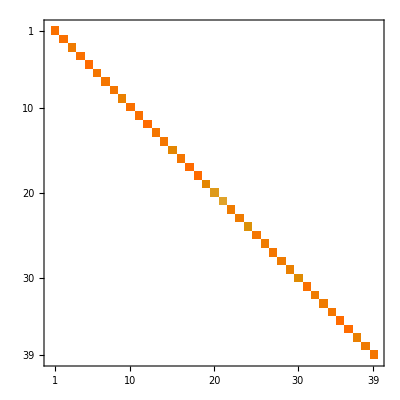

-Graphics-

```mathematica
Drop[Drop[zxDer2, {2, 3}], {4}].testWoop[[4;;]]//Threshold//MatrixPlot
Drop[Drop[zxDer2, {2, 3}], {4}].testWoop[[4;;]]//Threshold//MatrixPlot
```

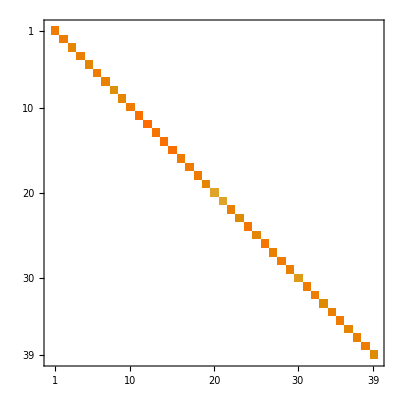

```mathematica
Drop[Drop[moop, {2, 3}], {4}].toostOons[[4;;]]//Threshold//MatrixPlot
```

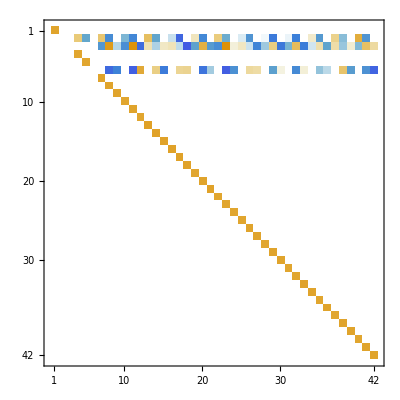

```mathematica
toostOons[[4;;]].Drop[Drop[moop, {2, 3}], {4}]//Threshold//MatrixPlot
```